```mathematica
SetDirectory[NotebookDirectory[]]
DE=y''[t]+100y[t]==36Cos[8t]
DSolve[DE, y[t], t]
ICS={y[0]==0, y'[0]==0}
sol=DSolve[{DE,ICS},y[t], t]
TeXForm[%]
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap03/mathematica

100 y[t]+y''[t]==36 Cos[8 t]

{{y[t]→Cos[8 t]+C[1] Cos[10 t]+C[2] Sin[10 t]}}

{y[0]==0,y'[0]==0}

{{y[t]→Cos[8 t]-Cos[10 t]}}

\{\{y(t)\to \cos (8 t)-\cos (10 t)\}\}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap03/mathematica

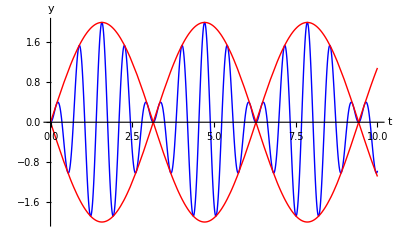

exercises-beats.pdf

```mathematica
plotspring1=Plot[{y[t]/.sol[[1]],2Sin[t], -2Sin[t]}, {t, 0, 10},AxesLabel->{"t","y"}, PlotStyle-> {{Blue,Thick},  {Red,Thick}, {Red,Thick}}]
Export["exercises-beats.pdf", plotspring1]
```

```mathematica
Maximize[(Cos[8 t]-Cos[10 t]), x]
```

{Cos[8 t]-Cos[10 t],{x→-12/5}}

```mathematica
Maximize[{Cos[8 t]-Cos[10 t],0≤t≤10},t]
```

{2,{t→π/2}}

```mathematica
ODE=y''[t]+4 y'[t]+20 y[t]==0
IC={y[0]==1/2, y'[0]==1}
parsol=DSolve[{ODE,IC}, y[t], t]
```

20 y[t]+4 y'[t]+y''[t]==0

{y[0]==1/2,y'[0]==1}

{{y[t]→1/2 ⅇ^(-2 t) (Cos[4 t]+Sin[4 t])}}

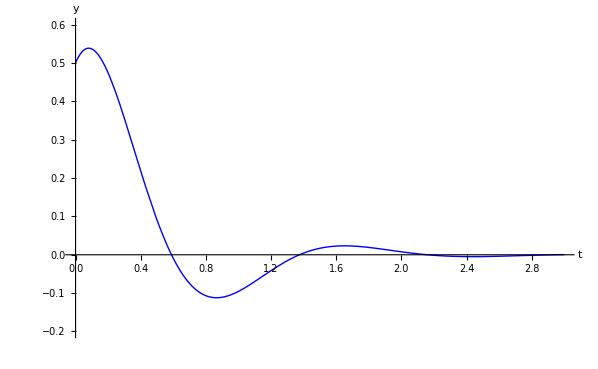

solution-through-equilibrium.pdf

```mathematica
plotspring2=Plot[y[t]/.parsol[[1]], {t, 0, 3},PlotRange->{{0, 3}, {-.2,.6}}, AxesLabel->{"t","y"}, PlotStyle-> {{Blue,Thick},  {Red,Thick}, {Red,Thick}}]
Export["solution-through-equilibrium.pdf", plotspring2]
```

```mathematica
N[3π/2]
```

4.71239

```mathematica
Solve[Cos[4 t]+Sin[4 t]==0, t]
```

{{t→ConditionalExpression[1/4 (-π/4+2 π C[1]), C[1]∈ℤ]},{t→ConditionalExpression[1/4 ((3 π)/4+2 π C[1]), C[1]∈ℤ]}}